# Paquet d’onde quantique: Ex1

```mathematica
Clear["Global`*"]
```

## Les hypothèses fondamantales de la mécanique quantique

Hypothèse de Planck: E=h ν=(2 π ω ℏ)/(2 π)=ℏω⟹ω=Ε/ℏ

Hypothèse de Louis De Broglie: λ=h/p=(2 π ℏ)/((2 π)/k)=ℏk⟹k=p/ℏ

Une solution mathématique de l' équation de Schrödinger:

```mathematica
ⅇ^(ⅈ (k x - ω t))/.k-> p/ℏ/.ω-> Ε/ℏ
```

ⅇ^(ⅈ ((p x)/ℏ-(t Ε)/ℏ))

## Paquet d’onde

La distribution spectrale des amplitudes:

```mathematica
Subscript[p, 0]:=2;α:=4;ϕ[p_]=(8/π)^(1/4)ⅇ^(-α (p-Subscript[p, 0])^2)
```

(2^(3/4) ⅇ^(-4 (-2+p)^2))/π^(1/4)

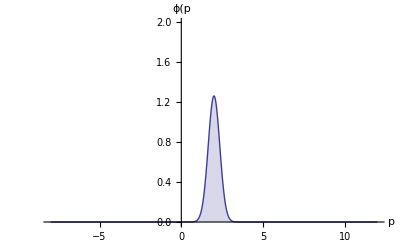

```mathematica
Plot[ϕ[p],{p,Subscript[p, 0]-10,Subscript[p, 0]+10},Filling->Axis,PlotRange->{0,2},AxesLabel->{"p","ϕ(p"}]
```

Relation de dispersion :

```mathematica
Ε[p_] =p^2/(2m)/.m-> 1
```

p^2/2

Fonction d’onde:

```mathematica
ψ[x_,t_]=1/(√(2π ℏ))∫_(-∞)^∞ ϕ[p] ⅇ^(ⅈ (p x-Ε[p] t)/ℏ)ⅆp/.ℏ-> 1;
```

```mathematica
Animate[Plot[Re[ψ[x,t]],{x,-10,200},PlotRange->{-0.5,0.5},AxesLabel->{"t","Re[ψ(x,t)]"}],{t,0,150,0.01},AnimationRunning->False]
```

Densité de probabilité de présence:

C'est le densité de probabilité de présence qui est significatif

```mathematica
P[x_,t_]=ψ[x,t]ψ[x,t]*;
```

```mathematica
Animate[Plot[P[x,t],{x,-10,200},PlotRange->{-0.5,0.5},AxesLabel->{"t","P(x,t)"}],{t,0,150,0.1},AnimationRunning->False]
```

## Le principe d’incertitude de Heisenberg

### Dans l’ espace de x

```mathematica
t:=0
```

```mathematica
P[x_]=P[x,t];
```

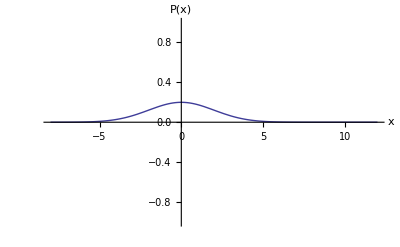

```mathematica
Plot[P[x],{x,Subscript[p, 0]-10,Subscript[p, 0]+10},PlotRange->{-1,1},AxesLabel->{"x","P(x)"}]
```

Densité de probabilité

```mathematica
∫_(-∞)^∞ P[x] ⅆx//N
```

1.

Moyenne de x

```mathematica
⟨x⟩=∫_(-∞)^∞ x P[x] ⅆx;
```

Moyenne de x^2

```mathematica
⟨x^2⟩=∫_(-∞)^∞ x^2 P[x]ⅆx;
```

Incertitude sur la valeur de x

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)//N
```

2.

### Dans l’ espace de p

```mathematica
P[p_]=ϕ[p]ϕ[p]*;
```

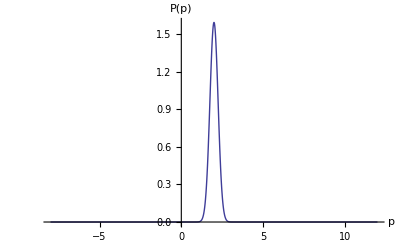

```mathematica
Plot[P[p],{p,Subscript[p, 0]-10,Subscript[p, 0]+10},PlotRange->All,AxesLabel->{"p","P(p)"}]
```

Densité de probabilité

```mathematica
∫_(-∞)^∞ P[p] ⅆp//N
```

1.

Moyenne de x

```mathematica
⟨p⟩=∫_(-∞)^∞ p P[p] ⅆp;
```

Moyenne de x^2

```mathematica
⟨p^2⟩=∫_(-∞)^∞ p^2 P[p] ⅆp;
```

Incertitude sur la valeur p

```mathematica
Δp=√(⟨p^2⟩-⟨p⟩^2)//N
```

0.25

### Le principe d’incertitude de Heisenberg

```mathematica
Δx Δp//N
```

0.5

## Vitesse

Vitesse de phase (m/s)

```mathematica
Subscript[v, ϕ]=Ε[p]/p
```

p/2

```mathematica
Table[Subscript[v, ϕ],{p,1,10}]
```

{1/2,1,3/2,2,5/2,3,7/2,4,9/2,5}

Vitesse de groupe (m/s)

```mathematica
Subscript[v, g]=D[Ε[p],p]/.p->Subscript[p, 0]
```

2